# Numbers as Qubits, Qubit Factorization, Tensor Products and Tensor Powers

by José Luis Gómez-Muñoz
http://homepage.cem.itesm.mx/lgomez/quantum/
jose.luis.gomez@itesm.mx

## Introduction

This is a tutorial on the use of Quantum`Computing` Mathematica add-on to work with binary qubits, tensor products and tensor powers

## Load the Package

First load the Quantum`Computing` package. Write:
Needs["Quantum`Computing`"];
then press at the same time the keys ⇧-⌤ to evaluate. Mathematica will load the package:

```mathematica
Needs["Quantum`Computing`"]
```

Quantum`Computing` Version 2.2.0. (July 2010) 
A Mathematica package for Quantum Computing in Dirac bra-ket notation and plotting of quantum circuits
by José Luis Gómez-Muñoz

Execute SetComputingAliases[] in order to use the keyboard to enter quantum objects in Dirac's notation
SetComputingAliases[] must be executed again in each new notebook that is created

In order to use the keyboard to enter quantum objects write:
SetComputingAliases[ ];
then press at the same time the keys ⇧-⌤ to evaluate. The semicolon prevents Mathematica from printing the help message. Remember that SetComputingAliases[ ] must be evaluated again in each new notebook:

```mathematica
SetComputingAliases[];
```

## From Decimal to Binary Numbers

In order to represent a 9 as a binary number made of 5 qubits, press the keys:
[ESC]toqb[ESC] [TAB] 9  [TAB] 5
then press at the same time the keys ⇧-⌤ to evaluate:

```mathematica
(|9⟩)_5
```

|0_OverHat[1],1_OverHat[2],0_OverHat[3],0_OverHat[4],1_OverHat[5]⟩

This is the "InputForm" version of the same calculation:

```mathematica
DecToQubit[9,5]
```

|0_OverHat[1],1_OverHat[2],0_OverHat[3],0_OverHat[4],1_OverHat[5]⟩

Copy-paste the previous output as argument of QubitToDec in order to get back the original number:

```mathematica
QubitToDec[|Subscript[0, OverHat[1]],Subscript[1, OverHat[2]],Subscript[0, OverHat[3]],Subscript[0, OverHat[4]],Subscript[1, OverHat[5]]⟩]
```

9

It can be specified which qubit label sould be used for each binary digit:

```mathematica
(|9⟩)_{10,20,100,200,250}
```

|0_OverHat[10],1_OverHat[20],0_OverHat[100],0_OverHat[200],1_OverHat[250]⟩

Qubit labels that are not integers can be used. Press [ESC]qb[ESC] to obtain the qubit template OverHat[□]:

```mathematica
(|9⟩)_{â,b̂,ĉ,d̂,ê}
```

|0_(â),1_(b̂),0_(ĉ),0_(d̂),1_(ê)⟩

This notation can take advantage of standard Mathematica commands that generate lists, like Range[]:

```mathematica
(|9⟩)_Range[12,24,3]
```

|0_OverHat[12],1_OverHat[15],0_OverHat[18],0_OverHat[21],1_OverHat[24]⟩

The "Quantum Register" template [ESC]qr[ESC] works very similar to the standard Mathematica command Range, with the extra advantage that we can specify a "prefix" for naming all the qubits:

```mathematica
(|9⟩)_ℛℯℊ𝒾𝓈𝓉ℯ𝓇[12,24,3,"w"]
```

|0_OverHat[w12],1_OverHat[w15],0_OverHat[w18],0_OverHat[w21],1_OverHat[w24]⟩

The "Quantum Register" template [ESC]qr[ESC] works very similar to the standard Mathematica command Range, with the extra advantage that we can specify a "prefix" for naming all the qubits:

```mathematica
(|9⟩)_ℛℯℊ𝒾𝓈𝓉ℯ𝓇[7,"w"]
```

|0_OverHat[w1],0_OverHat[w2],0_OverHat[w3],1_OverHat[w4],0_OverHat[w5],0_OverHat[w6],1_OverHat[w7]⟩

Here we generate a state of ten qubits, with all the qubits equal to zero except the "third" one. Press the keys [ESC]toqb[ESC]  to obtain the "decimal to binary" template:

```mathematica
(|2^(10-3)⟩)_10
```

|0_OverHat[1],0_OverHat[2],1_OverHat[3],0_OverHat[4],0_OverHat[5],0_OverHat[6],0_OverHat[7],0_OverHat[8],0_OverHat[9],0_OverHat[10]⟩

Here we generate a state of fifteen qubits, with all the qubits equal to zero except the "second" and "fifth" qubits. Press the keys [ESC]toqb[ESC]  to obtain the "decimal to binary" template:

```mathematica
(|2^(15-2)+2^(15-5)⟩)_15
```

|0_OverHat[1],1_OverHat[2],0_OverHat[3],0_OverHat[4],1_OverHat[5],0_OverHat[6],0_OverHat[7],0_OverHat[8],0_OverHat[9],0_OverHat[10],0_OverHat[11],0_OverHat[12],0_OverHat[13],0_OverHat[14],0_OverHat[15]⟩

Here we generate a state of fifteen qubits, with alternating zeros and ones. Press the keys [ESC]toqb[ESC]  to obtain the "decimal to binary" template and [ESC]si[ESC] to obtaing the "sigma notation sum" template:

```mathematica
(|∑_(j=1)^(15/2) 2^(15-2j)⟩)_15
```

|0_OverHat[1],1_OverHat[2],0_OverHat[3],1_OverHat[4],0_OverHat[5],1_OverHat[6],0_OverHat[7],1_OverHat[8],0_OverHat[9],1_OverHat[10],0_OverHat[11],1_OverHat[12],0_OverHat[13],1_OverHat[14],0_OverHat[15]⟩

This is a normalized, equally-weighted, linear combination of the computational basis kets for three qubits:

```mathematica
n=2^3;
1/(√n)∑_(j=0)^(n-1) (|j⟩)_Log[2,n]
```

1/(2 √2)(|0_OverHat[1],0_OverHat[2],0_OverHat[3]⟩+|0_OverHat[1],0_OverHat[2],1_OverHat[3]⟩+|0_OverHat[1],1_OverHat[2],0_OverHat[3]⟩+|0_OverHat[1],1_OverHat[2],1_OverHat[3]⟩+|1_OverHat[1],0_OverHat[2],0_OverHat[3]⟩+|1_OverHat[1],0_OverHat[2],1_OverHat[3]⟩+|1_OverHat[1],1_OverHat[2],0_OverHat[3]⟩+|1_OverHat[1],1_OverHat[2],1_OverHat[3]⟩)

This is a factorized version of the ket. It has to be wrapped by Hold, because the factorization is not "stable" under the algebraic rules of this Mathematica add-on:

```mathematica
n=2^3;
FactorKet[1/(√n)∑_(j=0)^(n-1) (|j⟩)_Log[2,n]]
```

Hold[(|0_OverHat[1]⟩+|1_OverHat[1]⟩)⊗(|0_OverHat[2]⟩+|1_OverHat[2]⟩)⊗(|0_OverHat[3]⟩+|1_OverHat[3]⟩)/(2 √2)]

Copy-paste the output of the previous command without the Hold[] "wrapper", and you obtain an expanded version:

```mathematica
(|Subscript[0, OverHat[1]]⟩+|Subscript[1, OverHat[1]]⟩)⊗(|Subscript[0, OverHat[2]]⟩+|Subscript[1, OverHat[2]]⟩)⊗(|Subscript[0, OverHat[3]]⟩+|Subscript[1, OverHat[3]]⟩)/(2 √2)
```

(|0_OverHat[1],0_OverHat[2],0_OverHat[3]⟩+|0_OverHat[1],0_OverHat[2],1_OverHat[3]⟩)/(2 √2)+(|0_OverHat[1],1_OverHat[2],0_OverHat[3]⟩+|0_OverHat[1],1_OverHat[2],1_OverHat[3]⟩)/(2 √2)+(|1_OverHat[1],0_OverHat[2],0_OverHat[3]⟩+|1_OverHat[1],0_OverHat[2],1_OverHat[3]⟩)/(2 √2)+(|1_OverHat[1],1_OverHat[2],0_OverHat[3]⟩+|1_OverHat[1],1_OverHat[2],1_OverHat[3]⟩)/(2 √2)

CollectKet gives the answer in a different format: each ket multiplied (or divided) by a scalar:

```mathematica
CollectKet[(|Subscript[0, OverHat[1]]⟩+|Subscript[1, OverHat[1]]⟩)⊗(|Subscript[0, OverHat[2]]⟩+|Subscript[1, OverHat[2]]⟩)⊗(|Subscript[0, OverHat[3]]⟩+|Subscript[1, OverHat[3]]⟩)/(2 √2)]
```

(|0_OverHat[1],0_OverHat[2],0_OverHat[3]⟩)/(2 √2)+(|0_OverHat[1],0_OverHat[2],1_OverHat[3]⟩)/(2 √2)+(|0_OverHat[1],1_OverHat[2],0_OverHat[3]⟩)/(2 √2)+(|0_OverHat[1],1_OverHat[2],1_OverHat[3]⟩)/(2 √2)+(|1_OverHat[1],0_OverHat[2],0_OverHat[3]⟩)/(2 √2)+(|1_OverHat[1],0_OverHat[2],1_OverHat[3]⟩)/(2 √2)+(|1_OverHat[1],1_OverHat[2],0_OverHat[3]⟩)/(2 √2)+(|1_OverHat[1],1_OverHat[2],1_OverHat[3]⟩)/(2 √2)

## More on Qubit Factorization

Kets can be factorized in tensor products using the command FactorKet. The result is inside the standard Mathematica command Hold:

```mathematica
FactorKet[|Subscript[0, OverHat[1]],Subscript[0, OverHat[2]],Subscript[0, OverHat[3]]⟩+|Subscript[0, OverHat[1]],Subscript[0, OverHat[2]],Subscript[1, OverHat[3]]⟩]
```

Hold[|0_OverHat[1]⟩⊗|0_OverHat[2]⟩⊗(|0_OverHat[3]⟩+|1_OverHat[3]⟩)]

The standard Mathematica command ReleaseHold cancels the Hold  command, and the factorization evolves to a stable representation:

```mathematica
ReleaseHold[  Hold[|Subscript[0, OverHat[1]]⟩⊗|Subscript[0, OverHat[2]]⟩⊗(|Subscript[0, OverHat[3]]⟩+|Subscript[1, OverHat[3]]⟩)]  ]
```

|0_OverHat[1],0_OverHat[2],0_OverHat[3]⟩+|0_OverHat[1],0_OverHat[2],1_OverHat[3]⟩

A simple yet nice example of ket factorization:

```mathematica
n=2^4;
FactorKet[∑_(j=0)^(n-1) 1/(√n)(|j⟩)_Log[2,n]]
```

Hold[(|0_OverHat[1]⟩+|1_OverHat[1]⟩)⊗(|0_OverHat[2]⟩+|1_OverHat[2]⟩)⊗(|0_OverHat[3]⟩+|1_OverHat[3]⟩)⊗(1/4 (|0_OverHat[4]⟩+|1_OverHat[4]⟩))]

Copy-paste the output of the previous command without the Hold[] "wrapper", and you obtain a partially expanded version:

```mathematica
(|Subscript[0, OverHat[1]]⟩+|Subscript[1, OverHat[1]]⟩)⊗(|Subscript[0, OverHat[2]]⟩+|Subscript[1, OverHat[2]]⟩)⊗(|Subscript[0, OverHat[3]]⟩+|Subscript[1, OverHat[3]]⟩)⊗(1/4 (|Subscript[0, OverHat[4]]⟩+|Subscript[1, OverHat[4]]⟩))
```

1/4 (|0_OverHat[1],0_OverHat[2],0_OverHat[3],0_OverHat[4]⟩+|0_OverHat[1],0_OverHat[2],0_OverHat[3],1_OverHat[4]⟩)+1/4 (|0_OverHat[1],0_OverHat[2],1_OverHat[3],0_OverHat[4]⟩+|0_OverHat[1],0_OverHat[2],1_OverHat[3],1_OverHat[4]⟩)+1/4 (|0_OverHat[1],1_OverHat[2],0_OverHat[3],0_OverHat[4]⟩+|0_OverHat[1],1_OverHat[2],0_OverHat[3],1_OverHat[4]⟩)+1/4 (|0_OverHat[1],1_OverHat[2],1_OverHat[3],0_OverHat[4]⟩+|0_OverHat[1],1_OverHat[2],1_OverHat[3],1_OverHat[4]⟩)+1/4 (|1_OverHat[1],0_OverHat[2],0_OverHat[3],0_OverHat[4]⟩+|1_OverHat[1],0_OverHat[2],0_OverHat[3],1_OverHat[4]⟩)+1/4 (|1_OverHat[1],0_OverHat[2],1_OverHat[3],0_OverHat[4]⟩+|1_OverHat[1],0_OverHat[2],1_OverHat[3],1_OverHat[4]⟩)+1/4 (|1_OverHat[1],1_OverHat[2],0_OverHat[3],0_OverHat[4]⟩+|1_OverHat[1],1_OverHat[2],0_OverHat[3],1_OverHat[4]⟩)+1/4 (|1_OverHat[1],1_OverHat[2],1_OverHat[3],0_OverHat[4]⟩+|1_OverHat[1],1_OverHat[2],1_OverHat[3],1_OverHat[4]⟩)

Use FactorKetList to get a list of the factors:

```mathematica
n=2^4;
FactorKetList[∑_(j=0)^(n-1) 1/(√n)(|j⟩)_Log[2,n]]
```

{|0_OverHat[1]⟩+|1_OverHat[1]⟩,|0_OverHat[2]⟩+|1_OverHat[2]⟩,|0_OverHat[3]⟩+|1_OverHat[3]⟩,1/4 |0_OverHat[4]⟩+1/4 |1_OverHat[4]⟩}

A different example where the "factorization" is actually not very interesting

```mathematica
n=2^4;
FactorKet[∑_(j=0)^(n-1) 1/(√(n-j))(|j⟩)_Log[2,n]]
```

Hold[1/60060(|0_OverHat[1]⟩⊗|0_OverHat[2]⟩⊗|0_OverHat[3]⟩⊗(15015 |0_OverHat[4]⟩)+|1_OverHat[1]⟩⊗|0_OverHat[2]⟩⊗|0_OverHat[3]⟩⊗(15015 √2 |0_OverHat[4]⟩)+|0_OverHat[1]⟩⊗|1_OverHat[2]⟩⊗|0_OverHat[3]⟩⊗(10010 √3 |0_OverHat[4]⟩)+|1_OverHat[1]⟩⊗|1_OverHat[2]⟩⊗|0_OverHat[3]⟩⊗(30030 |0_OverHat[4]⟩)+|0_OverHat[1]⟩⊗|0_OverHat[2]⟩⊗|1_OverHat[3]⟩⊗(4290 √14 |0_OverHat[4]⟩)+|1_OverHat[1]⟩⊗|0_OverHat[2]⟩⊗|1_OverHat[3]⟩⊗(10010 √6 |0_OverHat[4]⟩)+|0_OverHat[1]⟩⊗|1_OverHat[2]⟩⊗|1_OverHat[3]⟩⊗(6006 √10 |0_OverHat[4]⟩)+|1_OverHat[1]⟩⊗|1_OverHat[2]⟩⊗|1_OverHat[3]⟩⊗(30030 √2 |0_OverHat[4]⟩)+|0_OverHat[1]⟩⊗|0_OverHat[2]⟩⊗|0_OverHat[3]⟩⊗(4004 √15 |1_OverHat[4]⟩)+|1_OverHat[1]⟩⊗|0_OverHat[2]⟩⊗|0_OverHat[3]⟩⊗(8580 √7 |1_OverHat[4]⟩)+|0_OverHat[1]⟩⊗|1_OverHat[2]⟩⊗|0_OverHat[3]⟩⊗(5460 √11 |1_OverHat[4]⟩)+|1_OverHat[1]⟩⊗|1_OverHat[2]⟩⊗|0_OverHat[3]⟩⊗(20020 √3 |1_OverHat[4]⟩)+|0_OverHat[1]⟩⊗|0_OverHat[2]⟩⊗|1_OverHat[3]⟩⊗(4620 √13 |1_OverHat[4]⟩)+|1_OverHat[1]⟩⊗|0_OverHat[2]⟩⊗|1_OverHat[3]⟩⊗(12012 √5 |1_OverHat[4]⟩)+|0_OverHat[1]⟩⊗|1_OverHat[2]⟩⊗|1_OverHat[3]⟩⊗(20020 |1_OverHat[4]⟩)+|1_OverHat[1]⟩⊗|1_OverHat[2]⟩⊗|1_OverHat[3]⟩⊗(60060 |1_OverHat[4]⟩))]

Copy-paste the output of the previous command without the Hold[] "wrapper", and you obtain a partially expanded version:

```mathematica
1/60060(|Subscript[0, OverHat[1]]⟩⊗|Subscript[0, OverHat[2]]⟩⊗|Subscript[0, OverHat[3]]⟩⊗(15015 |Subscript[0, OverHat[4]]⟩)+|Subscript[1, OverHat[1]]⟩⊗|Subscript[0, OverHat[2]]⟩⊗|Subscript[0, OverHat[3]]⟩⊗(15015 √2 |Subscript[0, OverHat[4]]⟩)+|Subscript[0, OverHat[1]]⟩⊗|Subscript[1, OverHat[2]]⟩⊗|Subscript[0, OverHat[3]]⟩⊗(10010 √3 |Subscript[0, OverHat[4]]⟩)+|Subscript[1, OverHat[1]]⟩⊗|Subscript[1, OverHat[2]]⟩⊗|Subscript[0, OverHat[3]]⟩⊗(30030 |Subscript[0, OverHat[4]]⟩)+|Subscript[0, OverHat[1]]⟩⊗|Subscript[0, OverHat[2]]⟩⊗|Subscript[1, OverHat[3]]⟩⊗(4290 √14 |Subscript[0, OverHat[4]]⟩)+|Subscript[1, OverHat[1]]⟩⊗|Subscript[0, OverHat[2]]⟩⊗|Subscript[1, OverHat[3]]⟩⊗(10010 √6 |Subscript[0, OverHat[4]]⟩)+|Subscript[0, OverHat[1]]⟩⊗|Subscript[1, OverHat[2]]⟩⊗|Subscript[1, OverHat[3]]⟩⊗(6006 √10 |Subscript[0, OverHat[4]]⟩)+|Subscript[1, OverHat[1]]⟩⊗|Subscript[1, OverHat[2]]⟩⊗|Subscript[1, OverHat[3]]⟩⊗(30030 √2 |Subscript[0, OverHat[4]]⟩)+|Subscript[0, OverHat[1]]⟩⊗|Subscript[0, OverHat[2]]⟩⊗|Subscript[0, OverHat[3]]⟩⊗(4004 √15 |Subscript[1, OverHat[4]]⟩)+|Subscript[1, OverHat[1]]⟩⊗|Subscript[0, OverHat[2]]⟩⊗|Subscript[0, OverHat[3]]⟩⊗(8580 √7 |Subscript[1, OverHat[4]]⟩)+|Subscript[0, OverHat[1]]⟩⊗|Subscript[1, OverHat[2]]⟩⊗|Subscript[0, OverHat[3]]⟩⊗(5460 √11 |Subscript[1, OverHat[4]]⟩)+|Subscript[1, OverHat[1]]⟩⊗|Subscript[1, OverHat[2]]⟩⊗|Subscript[0, OverHat[3]]⟩⊗(20020 √3 |Subscript[1, OverHat[4]]⟩)+|Subscript[0, OverHat[1]]⟩⊗|Subscript[0, OverHat[2]]⟩⊗|Subscript[1, OverHat[3]]⟩⊗(4620 √13 |Subscript[1, OverHat[4]]⟩)+|Subscript[1, OverHat[1]]⟩⊗|Subscript[0, OverHat[2]]⟩⊗|Subscript[1, OverHat[3]]⟩⊗(12012 √5 |Subscript[1, OverHat[4]]⟩)+|Subscript[0, OverHat[1]]⟩⊗|Subscript[1, OverHat[2]]⟩⊗|Subscript[1, OverHat[3]]⟩⊗(20020 |Subscript[1, OverHat[4]]⟩)+|Subscript[1, OverHat[1]]⟩⊗|Subscript[1, OverHat[2]]⟩⊗|Subscript[1, OverHat[3]]⟩⊗(60060 |Subscript[1, OverHat[4]]⟩))
```

1/60060(15015 |0_OverHat[1],0_OverHat[2],0_OverHat[3],0_OverHat[4]⟩+4004 √15 |0_OverHat[1],0_OverHat[2],0_OverHat[3],1_OverHat[4]⟩+4290 √14 |0_OverHat[1],0_OverHat[2],1_OverHat[3],0_OverHat[4]⟩+4620 √13 |0_OverHat[1],0_OverHat[2],1_OverHat[3],1_OverHat[4]⟩+10010 √3 |0_OverHat[1],1_OverHat[2],0_OverHat[3],0_OverHat[4]⟩+5460 √11 |0_OverHat[1],1_OverHat[2],0_OverHat[3],1_OverHat[4]⟩+6006 √10 |0_OverHat[1],1_OverHat[2],1_OverHat[3],0_OverHat[4]⟩+20020 |0_OverHat[1],1_OverHat[2],1_OverHat[3],1_OverHat[4]⟩+15015 √2 |1_OverHat[1],0_OverHat[2],0_OverHat[3],0_OverHat[4]⟩+8580 √7 |1_OverHat[1],0_OverHat[2],0_OverHat[3],1_OverHat[4]⟩+10010 √6 |1_OverHat[1],0_OverHat[2],1_OverHat[3],0_OverHat[4]⟩+12012 √5 |1_OverHat[1],0_OverHat[2],1_OverHat[3],1_OverHat[4]⟩+30030 |1_OverHat[1],1_OverHat[2],0_OverHat[3],0_OverHat[4]⟩+20020 √3 |1_OverHat[1],1_OverHat[2],0_OverHat[3],1_OverHat[4]⟩+30030 √2 |1_OverHat[1],1_OverHat[2],1_OverHat[3],0_OverHat[4]⟩+60060 |1_OverHat[1],1_OverHat[2],1_OverHat[3],1_OverHat[4]⟩)

CollectKet gives the answer in a different format: each ket multiplied (or divided) by a scalar:

```mathematica
CollectKet[1/60060(15015 |Subscript[0, OverHat[1]],Subscript[0, OverHat[2]],Subscript[0, OverHat[3]],Subscript[0, OverHat[4]]⟩+4004 √15 |Subscript[0, OverHat[1]],Subscript[0, OverHat[2]],Subscript[0, OverHat[3]],Subscript[1, OverHat[4]]⟩+4290 √14 |Subscript[0, OverHat[1]],Subscript[0, OverHat[2]],Subscript[1, OverHat[3]],Subscript[0, OverHat[4]]⟩+4620 √13 |Subscript[0, OverHat[1]],Subscript[0, OverHat[2]],Subscript[1, OverHat[3]],Subscript[1, OverHat[4]]⟩+10010 √3 |Subscript[0, OverHat[1]],Subscript[1, OverHat[2]],Subscript[0, OverHat[3]],Subscript[0, OverHat[4]]⟩+5460 √11 |Subscript[0, OverHat[1]],Subscript[1, OverHat[2]],Subscript[0, OverHat[3]],Subscript[1, OverHat[4]]⟩+6006 √10 |Subscript[0, OverHat[1]],Subscript[1, OverHat[2]],Subscript[1, OverHat[3]],Subscript[0, OverHat[4]]⟩+20020 |Subscript[0, OverHat[1]],Subscript[1, OverHat[2]],Subscript[1, OverHat[3]],Subscript[1, OverHat[4]]⟩+15015 √2 |Subscript[1, OverHat[1]],Subscript[0, OverHat[2]],Subscript[0, OverHat[3]],Subscript[0, OverHat[4]]⟩+8580 √7 |Subscript[1, OverHat[1]],Subscript[0, OverHat[2]],Subscript[0, OverHat[3]],Subscript[1, OverHat[4]]⟩+10010 √6 |Subscript[1, OverHat[1]],Subscript[0, OverHat[2]],Subscript[1, OverHat[3]],Subscript[0, OverHat[4]]⟩+12012 √5 |Subscript[1, OverHat[1]],Subscript[0, OverHat[2]],Subscript[1, OverHat[3]],Subscript[1, OverHat[4]]⟩+30030 |Subscript[1, OverHat[1]],Subscript[1, OverHat[2]],Subscript[0, OverHat[3]],Subscript[0, OverHat[4]]⟩+20020 √3 |Subscript[1, OverHat[1]],Subscript[1, OverHat[2]],Subscript[0, OverHat[3]],Subscript[1, OverHat[4]]⟩+30030 √2 |Subscript[1, OverHat[1]],Subscript[1, OverHat[2]],Subscript[1, OverHat[3]],Subscript[0, OverHat[4]]⟩+60060 |Subscript[1, OverHat[1]],Subscript[1, OverHat[2]],Subscript[1, OverHat[3]],Subscript[1, OverHat[4]]⟩)]
```

1/4 |0_OverHat[1],0_OverHat[2],0_OverHat[3],0_OverHat[4]⟩+(|0_OverHat[1],0_OverHat[2],0_OverHat[3],1_OverHat[4]⟩)/(√15)+(|0_OverHat[1],0_OverHat[2],1_OverHat[3],0_OverHat[4]⟩)/(√14)+(|0_OverHat[1],0_OverHat[2],1_OverHat[3],1_OverHat[4]⟩)/(√13)+(|0_OverHat[1],1_OverHat[2],0_OverHat[3],0_OverHat[4]⟩)/(2 √3)+(|0_OverHat[1],1_OverHat[2],0_OverHat[3],1_OverHat[4]⟩)/(√11)+(|0_OverHat[1],1_OverHat[2],1_OverHat[3],0_OverHat[4]⟩)/(√10)+1/3 |0_OverHat[1],1_OverHat[2],1_OverHat[3],1_OverHat[4]⟩+(|1_OverHat[1],0_OverHat[2],0_OverHat[3],0_OverHat[4]⟩)/(2 √2)+(|1_OverHat[1],0_OverHat[2],0_OverHat[3],1_OverHat[4]⟩)/(√7)+(|1_OverHat[1],0_OverHat[2],1_OverHat[3],0_OverHat[4]⟩)/(√6)+(|1_OverHat[1],0_OverHat[2],1_OverHat[3],1_OverHat[4]⟩)/(√5)+1/2 |1_OverHat[1],1_OverHat[2],0_OverHat[3],0_OverHat[4]⟩+(|1_OverHat[1],1_OverHat[2],0_OverHat[3],1_OverHat[4]⟩)/(√3)+(|1_OverHat[1],1_OverHat[2],1_OverHat[3],0_OverHat[4]⟩)/(√2)+|1_OverHat[1],1_OverHat[2],1_OverHat[3],1_OverHat[4]⟩

## Tensor Products

Press the following keyboard keys in order to obtain the template for the "tensor product of a qubit":
[ESC]tprodqb[ESC]
then press [TAB] several times to select the place holder (square) at the bottom of the template and write 1. Press [TAB] one more time to select the uppermost place holder and write 7. Finally press [TAB] one more time to select the place holder in the subscript and write 0. Press at the same time [SHIFT]-[ENTER] to evaluate:

```mathematica
⊗_(n=1)^7|Subscript[0, n̂]⟩
```

|0_OverHat[1],0_OverHat[2],0_OverHat[3],0_OverHat[4],0_OverHat[5],0_OverHat[6],0_OverHat[7]⟩

The result was the same as this large tensor product of qubits. Each qubit is entered with the keys [ESC]qket0[ESC] and each tensor-product symbol between the kets is entered with the keys [ESC]tp[ESC]:

```mathematica
|Subscript[0, OverHat[1]]⟩⊗|Subscript[0, OverHat[2]]⟩⊗|Subscript[0, OverHat[3]]⟩⊗|Subscript[0, OverHat[4]]⟩⊗|Subscript[0, OverHat[5]]⟩⊗|Subscript[0, OverHat[6]]⟩⊗|Subscript[0, OverHat[7]]⟩
```

|0_OverHat[1],0_OverHat[2],0_OverHat[3],0_OverHat[4],0_OverHat[5],0_OverHat[6],0_OverHat[7]⟩

The [ESC]tprodqb[ESC] template can be used with qubit values that depend on the subindex:

```mathematica
⊗_(n=5)^11|Subscript[(((-1)^n+1)/2), n̂]⟩
```

|0_OverHat[5],1_OverHat[6],0_OverHat[7],1_OverHat[8],0_OverHat[9],1_OverHat[10],0_OverHat[11]⟩

There are many different ways to obtain the same result in Mathematica, some of them closer to standard Mathematics notation and some of them closer to programming paradigms, like procedural programming or functional programming. Here the standard Mathematica commands Boole and EvenQ are used to generate the same output as in the previous example:

```mathematica
⊗_(n=5)^11|Subscript[Boole[EvenQ[n]], n̂]⟩
```

|0_OverHat[5],1_OverHat[6],0_OverHat[7],1_OverHat[8],0_OverHat[9],1_OverHat[10],0_OverHat[11]⟩

A useful generalization can be used in the "tensor product": Press the following keyboard keys in order to obtain the template for the "tensor product of a qubit":
[ESC]tprodqb[ESC]
then press [TAB] several times to select the place holder (square) at the bottom of the template and write 1. Press [TAB] one more time to select the uppermost place holder and write {1,3,8,10,20}. Finally press [TAB] one more time to select the place holder in the subscript and write 0. Press at the same time [SHIFT]-[ENTER] to evaluate:

```mathematica
⊗_(n=1)^{1,3,8,10,20}|Subscript[0, n̂]⟩
```

|0_OverHat[1],0_OverHat[3],0_OverHat[8],0_OverHat[10],0_OverHat[20]⟩

This notation can take advantage of standard Mathematica commands that generate lists, like Range[]:

```mathematica
⊗_(n=1)^Range[15,27,3]|Subscript[0, n̂]⟩
```

|0_OverHat[15],0_OverHat[18],0_OverHat[21],0_OverHat[24],0_OverHat[27]⟩

If  a value different form 1 is used in the "initial" value of n for this generalization, then this value is used as an "offset":

```mathematica
⊗_(n=5)^{1,3,8,10,20}|Subscript[0, n̂]⟩
```

|0_OverHat[5],0_OverHat[7],0_OverHat[12],0_OverHat[14],0_OverHat[24]⟩

The tensor product can be used to generate complex products, taking advantage of standard Mathematica commands like Mod:

```mathematica
⊗_(n=1)^{1,3,8,10,20}|Subscript[Mod[n+1,2], n̂]⟩
```

|0_OverHat[1],0_OverHat[3],1_OverHat[8],1_OverHat[10],1_OverHat[20]⟩

Here is the tensor product of an operator. This time the [ESC]tprod[ESC] template is used instead of [ESC]tprodqb[ESC]. Notice that the qubit labels now are "m", which is the dummy index that was used in the product:

```mathematica
⊗_(m=1)^2(a00|Subscript[0, m̂]⟩·⟨Subscript[0, m̂]|+a01|Subscript[0, m̂]⟩·⟨Subscript[1, m̂]|+a10|Subscript[1, m̂]⟩·⟨Subscript[0, m̂]|+a11|Subscript[1, m̂]⟩·⟨Subscript[1, m̂]|)
```

a00^2 |0_OverHat[1],0_OverHat[2]⟩·⟨0_OverHat[1],0_OverHat[2]|+a00 a10 |0_OverHat[1],1_OverHat[2]⟩·⟨0_OverHat[1],0_OverHat[2]|+a00 a10 |1_OverHat[1],0_OverHat[2]⟩·⟨0_OverHat[1],0_OverHat[2]|+a10^2 |1_OverHat[1],1_OverHat[2]⟩·⟨0_OverHat[1],0_OverHat[2]|+a00 a01 |0_OverHat[1],0_OverHat[2]⟩·⟨0_OverHat[1],1_OverHat[2]|+a00 a11 |0_OverHat[1],1_OverHat[2]⟩·⟨0_OverHat[1],1_OverHat[2]|+a01 a10 |1_OverHat[1],0_OverHat[2]⟩·⟨0_OverHat[1],1_OverHat[2]|+a10 a11 |1_OverHat[1],1_OverHat[2]⟩·⟨0_OverHat[1],1_OverHat[2]|+a00 a01 |0_OverHat[1],0_OverHat[2]⟩·⟨1_OverHat[1],0_OverHat[2]|+a01 a10 |0_OverHat[1],1_OverHat[2]⟩·⟨1_OverHat[1],0_OverHat[2]|+a00 a11 |1_OverHat[1],0_OverHat[2]⟩·⟨1_OverHat[1],0_OverHat[2]|+a10 a11 |1_OverHat[1],1_OverHat[2]⟩·⟨1_OverHat[1],0_OverHat[2]|+a01^2 |0_OverHat[1],0_OverHat[2]⟩·⟨1_OverHat[1],1_OverHat[2]|+a01 a11 |0_OverHat[1],1_OverHat[2]⟩·⟨1_OverHat[1],1_OverHat[2]|+a01 a11 |1_OverHat[1],0_OverHat[2]⟩·⟨1_OverHat[1],1_OverHat[2]|+a11^2 |1_OverHat[1],1_OverHat[2]⟩·⟨1_OverHat[1],1_OverHat[2]|

On the other hand, if the qubit is a constant (this time the subscripts are independent of the product dummy-index m) you get a different result, because it is now the repeated application of the same operator in the same qubit. Use the [ESC]tprod[ESC] template:

```mathematica
⊗_(m=1)^2(a00|Subscript[0, OverHat[1]]⟩·⟨Subscript[0, OverHat[1]]|+a01|Subscript[0, OverHat[1]]⟩·⟨Subscript[1, OverHat[1]]|+a10|Subscript[1, OverHat[1]]⟩·⟨Subscript[0, OverHat[1]]|+a11|Subscript[1, OverHat[1]]⟩·⟨Subscript[1, OverHat[1]]|)
```

a00^2 |0_OverHat[1]⟩·⟨0_OverHat[1]|+a01 a10 |0_OverHat[1]⟩·⟨0_OverHat[1]|+a00 a10 |1_OverHat[1]⟩·⟨0_OverHat[1]|+a10 a11 |1_OverHat[1]⟩·⟨0_OverHat[1]|+a00 a01 |0_OverHat[1]⟩·⟨1_OverHat[1]|+a01 a11 |0_OverHat[1]⟩·⟨1_OverHat[1]|+a01 a10 |1_OverHat[1]⟩·⟨1_OverHat[1]|+a11^2 |1_OverHat[1]⟩·⟨1_OverHat[1]|

In order to enter the tensor product of a quantum expression, press the keys:
[ESC]tprod[ESC]
Then press the [TAB] key one or more times to select the first "place holder" □, and press the keys:
j[TAB]1[TAB]3[TAB]
Then press the keys:
[ESC]cnot[ESC]
Then press the [TAB] key one or more times to select the first "place holder" □, and press the keys:
j [TAB] j+1
then press at the same time the keys ⇧-⌤ to evaluate:

```mathematica
⊗_(j=1)^3(𝒞^{ĵ})[Subscript[𝒩𝒪𝒯, OverHat[j+1]]]
```

𝒞^{OverHat[1]}[𝒩𝒪𝒯_OverHat[2]]·𝒞^{OverHat[2]}[𝒩𝒪𝒯_OverHat[3]]·𝒞^{OverHat[3]}[𝒩𝒪𝒯_OverHat[4]]

Here is the operator in Dirac notation:

```mathematica
QuantumEvaluate[⊗_(j=1)^3(𝒞^{ĵ})[Subscript[𝒩𝒪𝒯, OverHat[j+1]]]]
```

|0_OverHat[1],0_OverHat[2],0_OverHat[3],0_OverHat[4]⟩·⟨0_OverHat[1],0_OverHat[2],0_OverHat[3],0_OverHat[4]|+|0_OverHat[1],0_OverHat[2],0_OverHat[3],1_OverHat[4]⟩·⟨0_OverHat[1],0_OverHat[2],0_OverHat[3],1_OverHat[4]|+|0_OverHat[1],0_OverHat[2],1_OverHat[3],1_OverHat[4]⟩·⟨0_OverHat[1],0_OverHat[2],1_OverHat[3],0_OverHat[4]|+|0_OverHat[1],0_OverHat[2],1_OverHat[3],0_OverHat[4]⟩·⟨0_OverHat[1],0_OverHat[2],1_OverHat[3],1_OverHat[4]|+|0_OverHat[1],1_OverHat[2],1_OverHat[3],0_OverHat[4]⟩·⟨0_OverHat[1],1_OverHat[2],0_OverHat[3],0_OverHat[4]|+|0_OverHat[1],1_OverHat[2],1_OverHat[3],1_OverHat[4]⟩·⟨0_OverHat[1],1_OverHat[2],0_OverHat[3],1_OverHat[4]|+|0_OverHat[1],1_OverHat[2],0_OverHat[3],1_OverHat[4]⟩·⟨0_OverHat[1],1_OverHat[2],1_OverHat[3],0_OverHat[4]|+|0_OverHat[1],1_OverHat[2],0_OverHat[3],0_OverHat[4]⟩·⟨0_OverHat[1],1_OverHat[2],1_OverHat[3],1_OverHat[4]|+|1_OverHat[1],1_OverHat[2],0_OverHat[3],0_OverHat[4]⟩·⟨1_OverHat[1],0_OverHat[2],0_OverHat[3],0_OverHat[4]|+|1_OverHat[1],1_OverHat[2],0_OverHat[3],1_OverHat[4]⟩·⟨1_OverHat[1],0_OverHat[2],0_OverHat[3],1_OverHat[4]|+|1_OverHat[1],1_OverHat[2],1_OverHat[3],1_OverHat[4]⟩·⟨1_OverHat[1],0_OverHat[2],1_OverHat[3],0_OverHat[4]|+|1_OverHat[1],1_OverHat[2],1_OverHat[3],0_OverHat[4]⟩·⟨1_OverHat[1],0_OverHat[2],1_OverHat[3],1_OverHat[4]|+|1_OverHat[1],0_OverHat[2],1_OverHat[3],0_OverHat[4]⟩·⟨1_OverHat[1],1_OverHat[2],0_OverHat[3],0_OverHat[4]|+|1_OverHat[1],0_OverHat[2],1_OverHat[3],1_OverHat[4]⟩·⟨1_OverHat[1],1_OverHat[2],0_OverHat[3],1_OverHat[4]|+|1_OverHat[1],0_OverHat[2],0_OverHat[3],1_OverHat[4]⟩·⟨1_OverHat[1],1_OverHat[2],1_OverHat[3],0_OverHat[4]|+|1_OverHat[1],0_OverHat[2],0_OverHat[3],0_OverHat[4]⟩·⟨1_OverHat[1],1_OverHat[2],1_OverHat[3],1_OverHat[4]|

The TraditionalForm can be easier to read

```mathematica
TraditionalForm[QuantumEvaluate[⊗_(j=1)^3(𝒞^{ĵ})[Subscript[𝒩𝒪𝒯, OverHat[j+1]]]]]
```

|0000⟩⟨0000|+|0001⟩⟨0001|+|0011⟩⟨0010|+|0010⟩⟨0011|+|0110⟩⟨0100|+|0111⟩⟨0101|+|0101⟩⟨0110|+|0100⟩⟨0111|+|1100⟩⟨1000|+|1101⟩⟨1001|+|1111⟩⟨1010|+|1110⟩⟨1011|+|1010⟩⟨1100|+|1011⟩⟨1101|+|1001⟩⟨1110|+|1000⟩⟨1111|

The standard Mathematica commands TeXForm and TraditionalForm can be used to create an expression that can be copy-pasted to a TEX editor

```mathematica
TeXForm[TraditionalForm[QuantumEvaluate[⊗_(j=1)^3(𝒞^{ĵ})[Subscript[𝒩𝒪𝒯, OverHat[j+1]]]]]]
```

|0000\rangle \langle 0000|+|0001\rangle \langle 0001|+|0011\rangle \langle
   0010|+|0010\rangle \langle 0011|+|0110\rangle \langle 0100|+|0111\rangle \langle
   0101|+|0101\rangle \langle 0110|+|0100\rangle \langle 0111|+|1100\rangle \langle
   1000|+|1101\rangle \langle 1001|+|1111\rangle \langle 1010|+|1110\rangle \langle
   1011|+|1010\rangle \langle 1100|+|1011\rangle \langle 1101|+|1001\rangle \langle
   1110|+|1000\rangle \langle 1111|

Here is a partial trace of the operator with respect to the second qubit. In order to enter the partial trace template press the keys:
[ESC]trace[ESC]
Then press the [TAB] key and write the qubit, then the [TAB] key and write the operator:

```mathematica
QuantumEvaluate[Subscript[Tr, OverHat[2]][⊗_(j=1)^3(𝒞^{ĵ})[Subscript[𝒩𝒪𝒯, OverHat[j+1]]]]]
```

|0_OverHat[1],0_OverHat[3],0_OverHat[4]⟩·⟨0_OverHat[1],0_OverHat[3],0_OverHat[4]|+|0_OverHat[1],1_OverHat[3],0_OverHat[4]⟩·⟨0_OverHat[1],0_OverHat[3],0_OverHat[4]|+|0_OverHat[1],0_OverHat[3],1_OverHat[4]⟩·⟨0_OverHat[1],0_OverHat[3],1_OverHat[4]|+|0_OverHat[1],1_OverHat[3],1_OverHat[4]⟩·⟨0_OverHat[1],0_OverHat[3],1_OverHat[4]|+|0_OverHat[1],0_OverHat[3],1_OverHat[4]⟩·⟨0_OverHat[1],1_OverHat[3],0_OverHat[4]|+|0_OverHat[1],1_OverHat[3],1_OverHat[4]⟩·⟨0_OverHat[1],1_OverHat[3],0_OverHat[4]|+|0_OverHat[1],0_OverHat[3],0_OverHat[4]⟩·⟨0_OverHat[1],1_OverHat[3],1_OverHat[4]|+|0_OverHat[1],1_OverHat[3],0_OverHat[4]⟩·⟨0_OverHat[1],1_OverHat[3],1_OverHat[4]|

Here is the quantum circuit that represents the gates:

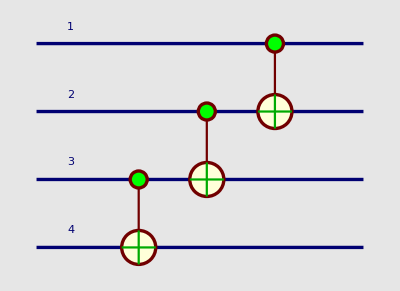

```mathematica
QuantumPlot[⊗_(j=1)^3(𝒞^{ĵ})[Subscript[𝒩𝒪𝒯, OverHat[j+1]]]]
```

A tridimensitonal representation of the circuit:

```mathematica
QuantumPlot3D[⊗_(j=1)^3(𝒞^{ĵ})[Subscript[𝒩𝒪𝒯, OverHat[j+1]]]]
```

-Graphics3D-

## Tensor Powers

Press the following keyboard keys in order to obtain the template for the "tensor power of a qubit":
[ESC]tpowqb[ESC]
then press [TAB] several times to select the largest place holder (square) and write 0. Press [TAB] one more time to select the small place holder in the subindex and write 1. Finally press [TAB] one more time to select the place holder in the exponent and write 7. Press at the same time [SHIFT]-[ENTER] to evaluate:

```mathematica
(|Subscript[0, OverHat[1]]⟩)^(⊗7)
```

|0_OverHat[1],0_OverHat[2],0_OverHat[3],0_OverHat[4],0_OverHat[5],0_OverHat[6],0_OverHat[7]⟩

If a number different from one is written in the subindex of the tensor power of a qubit, then that number is taken as the starting qubit:

```mathematica
(|Subscript[0, OverHat[5]]⟩)^(⊗7)
```

|0_OverHat[5],0_OverHat[6],0_OverHat[7],0_OverHat[8],0_OverHat[9],0_OverHat[10],0_OverHat[11]⟩

If a list of nonrepeated integers is given in the exponent, those integers are used as channels (qubits). The list of channels (qubits) must have the standard list delimiters of Mathematica, the curly brackets {}.

```mathematica
(|Subscript[0, OverHat[1]]⟩)^(⊗{1,3,8,10,20})
```

|0_OverHat[1],0_OverHat[3],0_OverHat[8],0_OverHat[10],0_OverHat[20]⟩

This notation can take advantage of standard Mathematica commands that generate lists, like Range[]:

```mathematica
(|Subscript[0, OverHat[1]]⟩)^(⊗Range[15,27,3])
```

|0_OverHat[15],0_OverHat[18],0_OverHat[21],0_OverHat[24],0_OverHat[27]⟩

If a number different from one is written in the subindex, then a constant is added to all the integers in the list such that qubit 1 becomes the qubit specified in the subindex:

```mathematica
(|Subscript[0, OverHat[5]]⟩)^(⊗{1,3,8,10,20})
```

|0_OverHat[5],0_OverHat[7],0_OverHat[12],0_OverHat[14],0_OverHat[24]⟩

The "tensor power" of more elaborated expresions can be calculated. It corresponds to have in each qubit the same superposition of 0 and 1, and the total state is the tensor product of all the superpositions. 
In order to obtain the template for the "tensor power", press the following keys:
[ESC]tpow[ESC]
then press [TAB] one or two times to select the largest place holder (square) and press:
a[ESC]qket[ESC]+b[ESC]qket[ESC]
then press [TAB] several times to select the first place holder and press
0[TAB]1[TAB]1[TAB]1[TAB]3
Finally press at the same time [SHIFT]-[ENTER] to evaluate.

```mathematica
(a|Subscript[0, OverHat[1]]⟩+b|Subscript[1, OverHat[1]]⟩)^(⊗3)
```

a^3 |0_OverHat[1],0_OverHat[2],0_OverHat[3]⟩+a^2 b |0_OverHat[1],0_OverHat[2],1_OverHat[3]⟩+a^2 b |0_OverHat[1],1_OverHat[2],0_OverHat[3]⟩+a b^2 |0_OverHat[1],1_OverHat[2],1_OverHat[3]⟩+a^2 b |1_OverHat[1],0_OverHat[2],0_OverHat[3]⟩+a b^2 |1_OverHat[1],0_OverHat[2],1_OverHat[3]⟩+a b^2 |1_OverHat[1],1_OverHat[2],0_OverHat[3]⟩+b^3 |1_OverHat[1],1_OverHat[2],1_OverHat[3]⟩

The result was the same as this large product of qubits:

```mathematica
Expand[(a|Subscript[0, OverHat[1]]⟩+b|Subscript[1, OverHat[1]]⟩)⊗(a|Subscript[0, OverHat[2]]⟩+b|Subscript[1, OverHat[2]]⟩)⊗(a|Subscript[0, OverHat[3]]⟩+b|Subscript[1, OverHat[3]]⟩)]
```

a^3 |0_OverHat[1],0_OverHat[2],0_OverHat[3]⟩+a^2 b |0_OverHat[1],0_OverHat[2],1_OverHat[3]⟩+a^2 b |0_OverHat[1],1_OverHat[2],0_OverHat[3]⟩+a b^2 |0_OverHat[1],1_OverHat[2],1_OverHat[3]⟩+a^2 b |1_OverHat[1],0_OverHat[2],0_OverHat[3]⟩+a b^2 |1_OverHat[1],0_OverHat[2],1_OverHat[3]⟩+a b^2 |1_OverHat[1],1_OverHat[2],0_OverHat[3]⟩+b^3 |1_OverHat[1],1_OverHat[2],1_OverHat[3]⟩

A starting qubit and a specific list of qubits can be given:

```mathematica
(a|Subscript[0, OverHat[101]]⟩+b|Subscript[1, OverHat[101]]⟩)^(⊗{2,6,7})
```

a^3 |0_OverHat[102],0_OverHat[106],0_OverHat[107]⟩+a^2 b |0_OverHat[102],0_OverHat[106],1_OverHat[107]⟩+a^2 b |0_OverHat[102],1_OverHat[106],0_OverHat[107]⟩+a b^2 |0_OverHat[102],1_OverHat[106],1_OverHat[107]⟩+a^2 b |1_OverHat[102],0_OverHat[106],0_OverHat[107]⟩+a b^2 |1_OverHat[102],0_OverHat[106],1_OverHat[107]⟩+a b^2 |1_OverHat[102],1_OverHat[106],0_OverHat[107]⟩+b^3 |1_OverHat[102],1_OverHat[106],1_OverHat[107]⟩

Here is the "tensor power" of an operator. Remember that [ESC]tpow[ESC] has to be used to write the "tensor power" template and [ESC]qketbra[ESC] to write the "one qubit operator element" template.

```mathematica
Expand[(a00|Subscript[0, OverHat[1]]⟩·⟨Subscript[0, OverHat[1]]|+a01|Subscript[0, OverHat[1]]⟩·⟨Subscript[1, OverHat[1]]|+a10|Subscript[1, OverHat[1]]⟩·⟨Subscript[0, OverHat[1]]|+a11|Subscript[1, OverHat[1]]⟩·⟨Subscript[1, OverHat[1]]|)^(⊗2)]
```

a00^2 |0_OverHat[1],0_OverHat[2]⟩·⟨0_OverHat[1],0_OverHat[2]|+a00 a10 |0_OverHat[1],1_OverHat[2]⟩·⟨0_OverHat[1],0_OverHat[2]|+a00 a10 |1_OverHat[1],0_OverHat[2]⟩·⟨0_OverHat[1],0_OverHat[2]|+a10^2 |1_OverHat[1],1_OverHat[2]⟩·⟨0_OverHat[1],0_OverHat[2]|+a00 a01 |0_OverHat[1],0_OverHat[2]⟩·⟨0_OverHat[1],1_OverHat[2]|+a00 a11 |0_OverHat[1],1_OverHat[2]⟩·⟨0_OverHat[1],1_OverHat[2]|+a01 a10 |1_OverHat[1],0_OverHat[2]⟩·⟨0_OverHat[1],1_OverHat[2]|+a10 a11 |1_OverHat[1],1_OverHat[2]⟩·⟨0_OverHat[1],1_OverHat[2]|+a00 a01 |0_OverHat[1],0_OverHat[2]⟩·⟨1_OverHat[1],0_OverHat[2]|+a01 a10 |0_OverHat[1],1_OverHat[2]⟩·⟨1_OverHat[1],0_OverHat[2]|+a00 a11 |1_OverHat[1],0_OverHat[2]⟩·⟨1_OverHat[1],0_OverHat[2]|+a10 a11 |1_OverHat[1],1_OverHat[2]⟩·⟨1_OverHat[1],0_OverHat[2]|+a01^2 |0_OverHat[1],0_OverHat[2]⟩·⟨1_OverHat[1],1_OverHat[2]|+a01 a11 |0_OverHat[1],1_OverHat[2]⟩·⟨1_OverHat[1],1_OverHat[2]|+a01 a11 |1_OverHat[1],0_OverHat[2]⟩·⟨1_OverHat[1],1_OverHat[2]|+a11^2 |1_OverHat[1],1_OverHat[2]⟩·⟨1_OverHat[1],1_OverHat[2]|

Notice the difference between the previous "tensor power" [ESC]tpow[ESC] and the following "normal power" [ESC]po[ESC]:

```mathematica
Expand[(a00|Subscript[0, OverHat[1]]⟩·⟨Subscript[0, OverHat[1]]|+a01|Subscript[0, OverHat[1]]⟩·⟨Subscript[1, OverHat[1]]|+a10|Subscript[1, OverHat[1]]⟩·⟨Subscript[0, OverHat[1]]|+a11|Subscript[1, OverHat[1]]⟩·⟨Subscript[1, OverHat[1]]|)^2]
```

a00^2 |0_OverHat[1]⟩·⟨0_OverHat[1]|+a01 a10 |0_OverHat[1]⟩·⟨0_OverHat[1]|+a00 a10 |1_OverHat[1]⟩·⟨0_OverHat[1]|+a10 a11 |1_OverHat[1]⟩·⟨0_OverHat[1]|+a00 a01 |0_OverHat[1]⟩·⟨1_OverHat[1]|+a01 a11 |0_OverHat[1]⟩·⟨1_OverHat[1]|+a01 a10 |1_OverHat[1]⟩·⟨1_OverHat[1]|+a11^2 |1_OverHat[1]⟩·⟨1_OverHat[1]|

Here is the "tensor power" of a quantum gate. Remember that [ESC]tpow[ESC] has to be used to write the "tensor power" template and [ESC]cnot[ESC] to write the "controlled-not" template.

```mathematica
((𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]])^(⊗3)
```

𝒞^{OverHat[1]}[𝒩𝒪𝒯_OverHat[2]]·𝒞^{OverHat[2]}[𝒩𝒪𝒯_OverHat[3]]·𝒞^{OverHat[3]}[𝒩𝒪𝒯_OverHat[4]]

The tensor power in Dirac notation:

```mathematica
QuantumEvaluate[((𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]])^(⊗3)]
```

|0_OverHat[1],0_OverHat[2],0_OverHat[3],0_OverHat[4]⟩·⟨0_OverHat[1],0_OverHat[2],0_OverHat[3],0_OverHat[4]|+|0_OverHat[1],0_OverHat[2],0_OverHat[3],1_OverHat[4]⟩·⟨0_OverHat[1],0_OverHat[2],0_OverHat[3],1_OverHat[4]|+|0_OverHat[1],0_OverHat[2],1_OverHat[3],1_OverHat[4]⟩·⟨0_OverHat[1],0_OverHat[2],1_OverHat[3],0_OverHat[4]|+|0_OverHat[1],0_OverHat[2],1_OverHat[3],0_OverHat[4]⟩·⟨0_OverHat[1],0_OverHat[2],1_OverHat[3],1_OverHat[4]|+|0_OverHat[1],1_OverHat[2],1_OverHat[3],0_OverHat[4]⟩·⟨0_OverHat[1],1_OverHat[2],0_OverHat[3],0_OverHat[4]|+|0_OverHat[1],1_OverHat[2],1_OverHat[3],1_OverHat[4]⟩·⟨0_OverHat[1],1_OverHat[2],0_OverHat[3],1_OverHat[4]|+|0_OverHat[1],1_OverHat[2],0_OverHat[3],1_OverHat[4]⟩·⟨0_OverHat[1],1_OverHat[2],1_OverHat[3],0_OverHat[4]|+|0_OverHat[1],1_OverHat[2],0_OverHat[3],0_OverHat[4]⟩·⟨0_OverHat[1],1_OverHat[2],1_OverHat[3],1_OverHat[4]|+|1_OverHat[1],1_OverHat[2],0_OverHat[3],0_OverHat[4]⟩·⟨1_OverHat[1],0_OverHat[2],0_OverHat[3],0_OverHat[4]|+|1_OverHat[1],1_OverHat[2],0_OverHat[3],1_OverHat[4]⟩·⟨1_OverHat[1],0_OverHat[2],0_OverHat[3],1_OverHat[4]|+|1_OverHat[1],1_OverHat[2],1_OverHat[3],1_OverHat[4]⟩·⟨1_OverHat[1],0_OverHat[2],1_OverHat[3],0_OverHat[4]|+|1_OverHat[1],1_OverHat[2],1_OverHat[3],0_OverHat[4]⟩·⟨1_OverHat[1],0_OverHat[2],1_OverHat[3],1_OverHat[4]|+|1_OverHat[1],0_OverHat[2],1_OverHat[3],0_OverHat[4]⟩·⟨1_OverHat[1],1_OverHat[2],0_OverHat[3],0_OverHat[4]|+|1_OverHat[1],0_OverHat[2],1_OverHat[3],1_OverHat[4]⟩·⟨1_OverHat[1],1_OverHat[2],0_OverHat[3],1_OverHat[4]|+|1_OverHat[1],0_OverHat[2],0_OverHat[3],1_OverHat[4]⟩·⟨1_OverHat[1],1_OverHat[2],1_OverHat[3],0_OverHat[4]|+|1_OverHat[1],0_OverHat[2],0_OverHat[3],0_OverHat[4]⟩·⟨1_OverHat[1],1_OverHat[2],1_OverHat[3],1_OverHat[4]|

Notice the difference between the previous "tensor power"  [ESC]tpow[ESC] and the following "normal power"  [ESC]po[ESC]:

```mathematica
QuantumEvaluate[((𝒞^{OverHat[1]})[𝒩𝒪𝒯[OverHat[2]]])^3]
```

|0_OverHat[1],0_OverHat[2]⟩·⟨0_OverHat[1],0_OverHat[2]|+|0_OverHat[1],1_OverHat[2]⟩·⟨0_OverHat[1],1_OverHat[2]|+|1_OverHat[1],1_OverHat[2]⟩·⟨1_OverHat[1],0_OverHat[2]|+|1_OverHat[1],0_OverHat[2]⟩·⟨1_OverHat[1],1_OverHat[2]|

Notice the difference between the "tensor power" [ESC]tpow[ESC] and the "normal power" [ESC]po[ESC]:

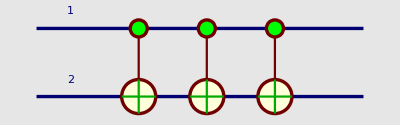
{-Graphics-,-Graphics-}

```mathematica
{QuantumPlot[((𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]])^(⊗3)],QuantumPlot[((𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]])^3,QuantumGatePowers->False]}
```

Here is a partial trace of the operator with respect to the second qubit. In order to enter the partial trace template press the keys:
[ESC]trace[ESC]
Then press the [TAB] key and write the qubit, then the [TAB] key and write the operator:

```mathematica
QuantumEvaluate[Subscript[Tr, OverHat[2]][((𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]])^(⊗3)]]
```

|0_OverHat[1],0_OverHat[3],0_OverHat[4]⟩·⟨0_OverHat[1],0_OverHat[3],0_OverHat[4]|+|0_OverHat[1],1_OverHat[3],0_OverHat[4]⟩·⟨0_OverHat[1],0_OverHat[3],0_OverHat[4]|+|0_OverHat[1],0_OverHat[3],1_OverHat[4]⟩·⟨0_OverHat[1],0_OverHat[3],1_OverHat[4]|+|0_OverHat[1],1_OverHat[3],1_OverHat[4]⟩·⟨0_OverHat[1],0_OverHat[3],1_OverHat[4]|+|0_OverHat[1],0_OverHat[3],1_OverHat[4]⟩·⟨0_OverHat[1],1_OverHat[3],0_OverHat[4]|+|0_OverHat[1],1_OverHat[3],1_OverHat[4]⟩·⟨0_OverHat[1],1_OverHat[3],0_OverHat[4]|+|0_OverHat[1],0_OverHat[3],0_OverHat[4]⟩·⟨0_OverHat[1],1_OverHat[3],1_OverHat[4]|+|0_OverHat[1],1_OverHat[3],0_OverHat[4]⟩·⟨0_OverHat[1],1_OverHat[3],1_OverHat[4]|

## Generalizations of the Tensor Power

Here is a useful generalization of the notation: If a list of 0s and 1s is given in the ket label, then each channel (qubit) takes the corresponding value. The list of 0s and 1s must use the standard list delimiters of Mathematica, the curly brackets {}. Remember that [ESC]tpowqb[ESC] has to be used to write the "tensor power of a qubit" template:

```mathematica
(|Subscript[{1,0,0,1}, OverHat[1]]⟩)^(⊗4)
```

|1_OverHat[1],0_OverHat[2],0_OverHat[3],1_OverHat[4]⟩

The result was the same as this tensor product of qubits:

```mathematica
|Subscript[1, OverHat[1]]⟩⊗|Subscript[0, OverHat[2]]⟩⊗|Subscript[0, OverHat[3]]⟩⊗|Subscript[1, OverHat[4]]⟩
```

|1_OverHat[1],0_OverHat[2],0_OverHat[3],1_OverHat[4]⟩

A starting qubit and a specific list of qubits can be given:

```mathematica
(|Subscript[{1,0,0,1}, OverHat[31]]⟩)^(⊗{1,2,6,7})
```

|1_OverHat[31],0_OverHat[32],0_OverHat[36],1_OverHat[37]⟩

Even a more general case can be generated if each element in the ket-label list is a pair of constants. Remember that [ESC]tpowqb[ESC] has to be used to write the "tensor power of a qubit" template:

```mathematica
(|Subscript[{{a0,a1},{b0,b1}}, OverHat[1]]⟩)^(⊗2)
```

a0 b1 |0_OverHat[1],1_OverHat[2]⟩+b0 (a0 |0_OverHat[1],0_OverHat[2]⟩+a1 |1_OverHat[1],0_OverHat[2]⟩)+a1 b1 |1_OverHat[1],1_OverHat[2]⟩

The result was the same as this tensor product of qubits:

```mathematica
(a0|Subscript[0, OverHat[1]]⟩+a1|Subscript[1, OverHat[1]]⟩)⊗(b0|Subscript[0, OverHat[2]]⟩+b1|Subscript[1, OverHat[2]]⟩)
```

a0 b1 |0_OverHat[1],1_OverHat[2]⟩+b0 (a0 |0_OverHat[1],0_OverHat[2]⟩+a1 |1_OverHat[1],0_OverHat[2]⟩)+a1 b1 |1_OverHat[1],1_OverHat[2]⟩

This is a very general example using the [ESC]tpowqb[ESC] template:

```mathematica
(|Subscript[{1,{b0,b1},0,{d0,d1}}, OverHat[20]]⟩)^(⊗{3,4,8,9})
```

b0 d1 |1_OverHat[22],0_OverHat[23],0_OverHat[27],1_OverHat[28]⟩+d0 (b0 |1_OverHat[22],0_OverHat[23],0_OverHat[27],0_OverHat[28]⟩+b1 |1_OverHat[22],1_OverHat[23],0_OverHat[27],0_OverHat[28]⟩)+b1 d1 |1_OverHat[22],1_OverHat[23],0_OverHat[27],1_OverHat[28]⟩

The result was the same as this tensor product of qubits:

```mathematica
|Subscript[1, OverHat[23]]⟩⊗(b0|Subscript[0, OverHat[24]]⟩+b1|Subscript[1, OverHat[24]]⟩)⊗|Subscript[0, OverHat[28]]⟩⊗(d0|Subscript[0, OverHat[29]]⟩+d1|Subscript[1, OverHat[29]]⟩)
```

b0 d1 |1_OverHat[23],0_OverHat[24],0_OverHat[28],1_OverHat[29]⟩+d0 (b0 |1_OverHat[23],0_OverHat[24],0_OverHat[28],0_OverHat[29]⟩+b1 |1_OverHat[23],1_OverHat[24],0_OverHat[28],0_OverHat[29]⟩)+b1 d1 |1_OverHat[23],1_OverHat[24],0_OverHat[28],1_OverHat[29]⟩

## Different Kinds of Products and Powers

Next table shows the different notations for "tensor products", "powers" and "normal powers". Notice the difference betwen a "normal power" a^n and a "tensor power" (a)^(⊗n). Notice also the difference when the argument of a "tensor product" depends on the dummy index ⊗_(m=1)^n a[m] and when it does not depend on the dummy index ⊗_(m=1)^n a

-Graphics-

by José Luis Gómez-Muñoz
http://homepage.cem.itesm.mx/lgomez/quantum/
jose.luis.gomez@itesm.mx